```mathematica
p=10;
s=0.05;
x1=0.25;
x2=0.35;
x3=0.5;
x4=0.6;
c1=p-1+1/x1;
c2=p-1+1/x2;
c3=p-1+1/x3;
c4=p-1+1/x4;
```

```mathematica
xappr1[t_]:=1/(c1*Exp[s*t]-p+1);
xappr2[t_]:=1/(c2*Exp[s*t]-p+1);
xappr3[t_]:=1/(c3*Exp[s*t]-p+1);
xappr4[t_]:=1/(c4*Exp[s*t]-p+1);
```

```mathematica
numeric1=NDSolve[{D[x[t],t]+s*(1+x[t]*p)*x[t]*(1-x[t])==0,x[0]==x1},x[t],{t,0,Infinity},MaxSteps->50000];
numeric2=NDSolve[{D[x[t],t]+s*(1+x[t]*p)*x[t]*(1-x[t])==0,x[0]==x2},x[t],{t,0,Infinity},MaxSteps->50000];
numeric3=NDSolve[{D[x[t],t]+s*(1+x[t]*p)*x[t]*(1-x[t])==0,x[0]==x3},x[t],{t,0,Infinity},MaxSteps->50000];
numeric4=NDSolve[{D[x[t],t]+s*(1+x[t]*p)*x[t]*(1-x[t])==0,x[0]==x4},x[t],{t,0,Infinity},MaxSteps->50000];
```

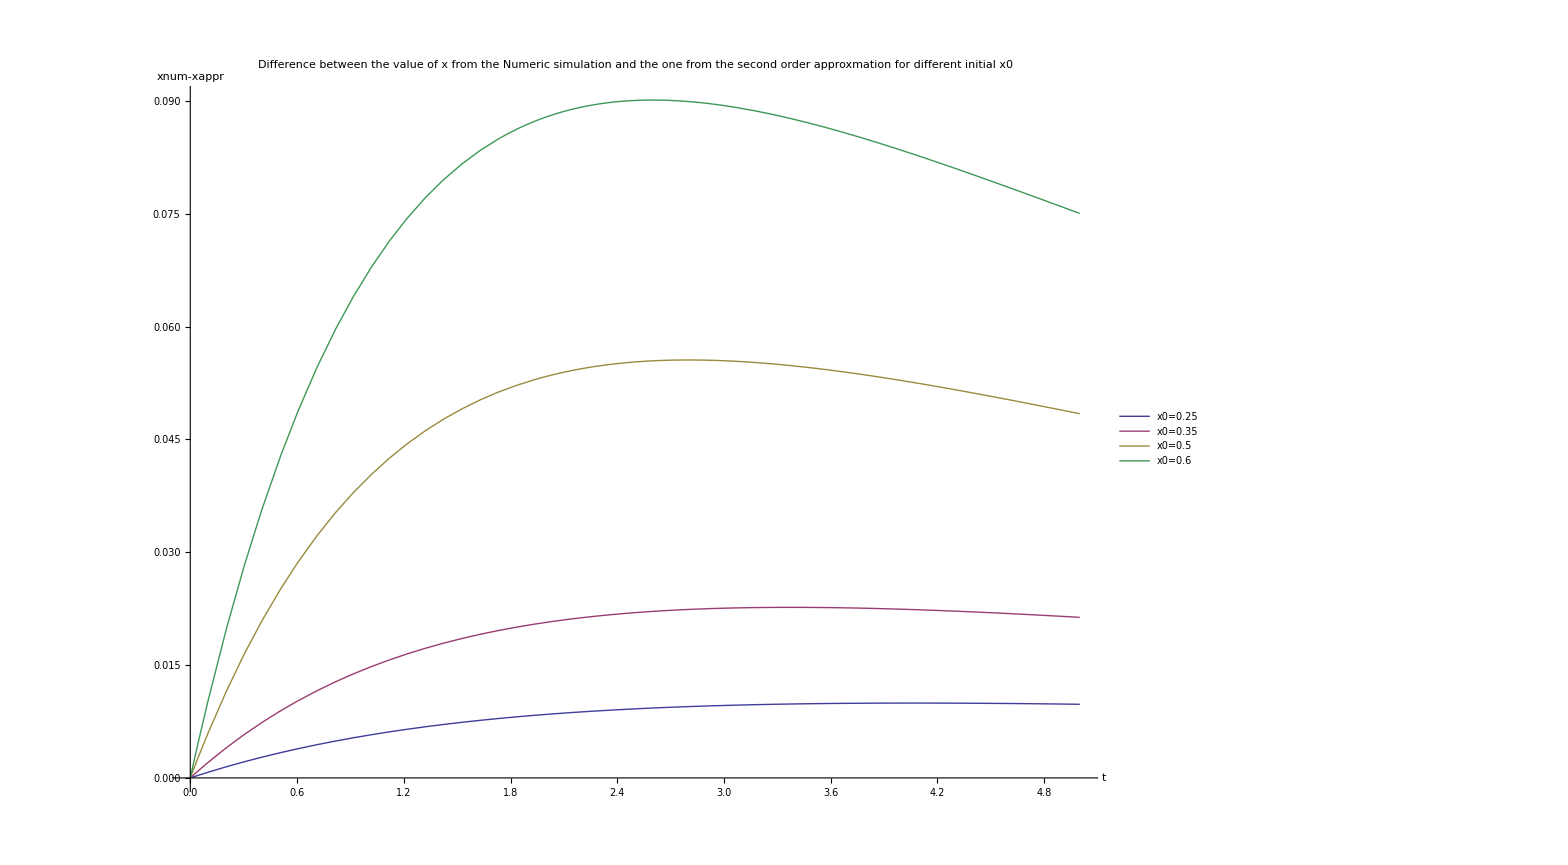

```mathematica
Plot[{Evaluate[x[t]/.numeric1]-Evaluate[xappr1[t]],Evaluate[x[t]/.numeric2]-Evaluate[xappr2[t]],Evaluate[x[t]/.numeric3]-Evaluate[xappr3[t]],Evaluate[x[t]/.numeric4]-Evaluate[xappr4[t]]},{t,0,5},PlotLegends->Placed[{"x0=0.25","x0=0.35","x0=0.5","x0=0.6"},{0.65,0.8}],AxesLabel->{"t","xnum-xappr"},PlotLabel->"Difference between the value of x from the Numeric simulation and the one from the second order approxmation for different initial x0",ImageSize->1400]
```